```mathematica
Quit[]
```

# Cagatay Duygu 48369962

## i. Find the controller-form state space realization using a suitable MFD.

```mathematica
G[s]=({{s/(s^2-9), 3/(s+1)}, {3/(s+3), 0.5/(s+2)}});
```

G (s) is  strictly proper!

```mathematica
H[s]=G[s]
```

{{s/(-9+s^2),3/(1+s)},{3/(3+s),0.5/(2+s)}}

### Useful functions (run the cell):

```mathematica
BlockDiagonalMatrix[b:{__?MatrixQ}]:=Module[{r,c,n=Length[b],i,j},{r,c}=Transpose[Dimensions/@b];
ArrayFlatten[Table[If[i==j,b[[i]],ConstantArray[0,{r[[i]],c[[j]]}]],{i,n},{j,n}]]];
FindMin[at_,kt_,xt_,pt_]:=Module[{a=at,k=kt,x=xt,p=pt,i,rgmin,degmin},For[i=k;rgmin=k;degmin=+Infinity,i≤p,i++,If[a[[i]]=!=0&&Exponent[a[[i]],x]<degmin,rgmin=i;
degmin=Exponent[a[[i]],x]]];
rgmin];

Variabile[at_]:=Module[{a=at,xt},xt=Variables[a];
If[xt==={},d,xt[[1]]]];

ExtPolQ[lt_List,xt_:{}]:=Module[{x=xt},
If[x==={}&&Length[Variables[lt]]>1,Message[General::badarg];
Return[$Failed],If[x==={},x=Variabile[lt]]];
(*If all the components of lt are polynomials in x*)Apply[And,PolynomialQ[#,x]&/@Flatten[lt]]||(*or in x^-1,the function returns True,False otherwise.(Substituting all the symbols x^-n->x^n we can use PolynomialQ also in this case)*)Apply[And,PolynomialQ[#,x]&/@Flatten[Expand[lt]/.{(x^(n:_))->(x^-n),x->x^-1}]]];

ExtendedHermiteForm[at_,xt_:{}]:=Module[{a=at,p,m,x=xt,u,v,k,kcl,i,j,q,deg,esp,coef,rg,rmin,upc,lpc,ch=False},If[x==={}&&Length[Variables[a]]>1,Message[General::badarg];
Return[$Failed],If[x==={},x=Variabile[a]]];
If[Not[ExtPolQ[a,x]],Message[General::pol];Return[$Failed]];
If[Not[Apply[And,PolynomialQ[#,x]&/@Flatten[a]]],a=a/.{(x^(n:_))->(x^-n)};
ch=True];
(*Initialize the variables*){p,m}=Dimensions[a];
u=IdentityMatrix[p];
(*Main loop on k (and kcl)*)For[k=1;kcl=1,k≤p&&kcl≤m,k++,(*Find the first non-zero element in row k*)While[a[[Range[k,p],kcl]]===Table[0,{p-k+1}]&&kcl<m,kcl++];
(*With this loop we eliminate all the elements in column kcl below position k*)While[If[k==p,False,a[[Range[k+1,p],kcl]]=!=Table[0,{p-k}]],(*Put the least degree element within column kcl in position (k,kcl)*)rmin=FindMin[Transpose[a][[kcl]],k,x,p];
If[rmin≠k,a=a/.{a[[rmin]]->a[[k]],a[[k]]->a[[rmin]]};
u=u/.{u[[rmin]]->u[[k]],u[[k]]->u[[rmin]]}];
(*Lower the degree of non-zero polynomials in column kcl below a[[k,kcl]]*)For[i=k+1,i≤p,i++,If[a[[i,kcl]]=!=0,lpc=PolynomialQuotient[a[[i,kcl]],a[[k,kcl]],x];
a=ReplacePart[a,Together[a[[i]]-a[[k]]*lpc],i];
u=ReplacePart[u,Expand[u[[i]]-u[[k]]*lpc],i]]]];(*Endwhile*)(*In column kcl lower the degree of polynomials above a[[k,kcl]] having the degree higher than that of a[[k,kcl]]*)If[a[[k,kcl]]=!=0,For[i=1,i<k,i++,If[a[[i,kcl]]=!=0,If[Exponent[a[[i,kcl]],x]≥Exponent[a[[k,kcl]],x],lpc=PolynomialQuotient[a[[i,kcl]],a[[k,kcl]],x];
a=ReplacePart[a,Together[a[[i]]-a[[k]]*lpc],i];
u=ReplacePart[u,Expand[u[[i]]-u[[k]]*lpc],i]]]]];
(*Make a[[k,kcl]] monic*)If[a[[k,kcl]]=!=0,lpc=Coefficient[a[[k,kcl]],x,Exponent[a[[k,kcl]],x]];
If[lpc=!=1,a=ReplacePart[a,Expand[a[[k]]/lpc],k];
u=ReplacePart[u,Expand[u[[k]]/lpc],k]]];
kcl++];(*Endfor*)(*Put all the zero rows in the last positions*)For[k=1,k<p,k++,If[a[[k]]===Table[0,{m}],i=p;
While[a[[i]]===Table[0,{m}]&&i>k,i=i-1];
If[i>k,For[j=k,j≤i,j++,a=ReplacePart[a,a[[j+1]],j];
u=ReplacePart[u,u[[j+1]],j]]];](*endif*)];(*endfor*)If[ch,{a,u}={a,u}/.{x^(n:_)->x^-n,x->x^-1}];
{a,u}]/;MatrixQ[at]||Message[General::mtrx,"ExtendedHermiteForm"];
```

SetDelayed::write: Tag BlockDiagonalMatrix in BlockDiagonalMatrix[b:{__?MatrixQ}] is Protected.

### Find the N(s) and D(s) for H(s) using the column common denominator method:

```mathematica
N1[s]=({{s, 3(s+2)}, {3(s-3), 0.5(s+1)}})//Chop;
D1[s]=({{s^2-9, 0}, {0, (s+1) (s+2)}})//Chop;
N1[s].Inverse[D1[s]]//Simplify //Chop
```

{{s/(-9+s^2),3/(1+s)},{3/(3+s),0.5/(2.+s)}}

```mathematica
H[s]==N1[s].Inverse[D1[s]]//Simplify
```

True

#### Get the minimal MFD :

```mathematica
DN[s]=Join[D1[s],N1[s]];
{h[s],U[s]}=ExtendedHermiteForm[DN[s],s];
h[s]//MatrixForm
```

(1 | 0.
0. | 1.
0 | 0
0 | 0)

```mathematica
Wg[s]=Take[h[s],2];
N2[s]=N1[s].Inverse[Wg[s]]//Simplify //Chop //Rationalize;
N2[s]//TraditionalForm
```

(s | 3 s+6
3 s-9 | s/2+1/2)

```mathematica
D2[s]=D1[s].Inverse[Wg[s]]//Simplify //Rationalize;
D2[s]//TraditionalForm
```

(s^2-9 | 0
0 | (s+1) (s+2))

#### Check the transfer function :

```mathematica
H2[s]=N2[s].Inverse[D2[s]]//Simplify
H[s]==H2[s]
```

{{s/(-9+s^2),3/(1+s)},{3/(3+s),1/(4+2 s)}}

{{s/(-9+s^2),3/(1+s)},{3/(3+s),0.5/(2+s)}}=={{s/(-9+s^2),3/(1+s)},{3/(3+s),1/(4+2 s)}}

Now the MFD realization will be minimal.

#### Build up S(s) and D_hc:

```mathematica
D2[s]//Expand
```

{{-9+s^2,0},{0,2+3 s+s^2}}

```mathematica
n=Length[D2[s]];
k=Table[Max[Exponent[D2[s]ᵀ[[i]],s]],{i,1,n}]
S[s]=DiagonalMatrix[s^k]
```

{2,2}

{{s^2,0},{0,s^2}}

```mathematica
Dhc=Coefficient[D2[s]ᵀ,s^k]ᵀ
```

{{1,0},{0,1}}

#### Build up ψ(s), L(s), and D_lc :

```mathematica
p2=Table[{Reverse[s^Range[0,k[[i]]-1]]},{i,1,n}]
```

{{{s,1}},{{s,1}}}

```mathematica
ψ[s]=BlockDiagonalMatrix[p2]ᵀ
```

Transpose[BlockDiagonalMatrix[{{{s,1}},{{s,1}}}]]

## BlockDiagonalMatrix function does not work in my file (it says it is protected.). Thus I will write those myself.

```mathematica
ψ[s]=({{s, 0}, {1, 0}, {0, s}, {0, 1}})
```

{{s,0},{1,0},{0,s},{0,1}}

```mathematica
L[s]=D2[s]-Dhc.S[s]//Expand
```

{{-9,0},{0,2+3 s}}

```mathematica
d2=Array[Subscript[d, ##]&,{n,Total[k]}];
sol1=SolveAlways[Thread[Flatten[L[s]]==Flatten[d2.ψ[s]]],s]//Flatten;
Dlc=d2/.sol1
```

{{0,-9,0,0},{0,0,3,2}}

#### Build up A_c^0:

```mathematica
Ai=Table[DiagonalMatrix[ConstantArray[1,Max[k[[i]]-1,1]],-1,k[[i]]],{i,1,n}]
Ac0=({{0, 0, 0, 0}, {1, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 1, 0}})
```

{{{0,0},{1,0}},{{0,0},{1,0}}}

{{0,0,0,0},{1,0,0,0},{0,0,0,0},{0,0,1,0}}

#### Build up B_c^0:

```mathematica
Bi=Table[{UnitVector[k[[i]],1]},{i,1,n}]
Bc0=({{1, 0}, {0, 0}, {0, 1}, {0, 0}})
```

{{{1,0}},{{1,0}}}

{{1,0},{0,0},{0,1},{0,0}}

#### Obtain the matrices for the controller - form state space realization :

```mathematica
Ac=Ac0-Bc0.Inverse[Dhc].Dlc;
Ac //MatrixForm
```

(0 | 9 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | -3 | -2
0 | 0 | 1 | 0)

```mathematica
Bc=Bc0.Inverse[Dhc];
Bc //MatrixForm
```

(1 | 0
0 | 0
0 | 1
0 | 0)

```mathematica
nlc2=Array[Subscript[nlc, ##]&,{Length[N2[s]],Total[k]}];
sol2=SolveAlways[Thread[Flatten[N2[s]]==Flatten[nlc2.ψ[s]]],s]//Flatten;
Cc=nlc2/.sol2
```

{{1,0,3,6},{3,-9,1/2,1/2}}

### State Space Representation :

```mathematica
x[t]=Array[Subscript[x, #][t]&,Total[k]]
y[t]=Array[Subscript[y, #][t]&,Length[N2[s]]]
u[t]=Array[Subscript[u, #][t]&,Length[Bcᵀ]]
```

{x_1[t],x_2[t],x_3[t],x_4[t]}

{y_1[t],y_2[t]}

{u_1[t],u_2[t]}

```mathematica
SEQ=Thread[D[x[t],t]==Ac.x[t]+Bc.u[t]];ColumnForm[SEQ]
OEQ=Thread[y[t]==Cc.x[t]];ColumnForm[OEQ]
```

x_1'[t]==u_1[t]+9 x_2[t]
x_2'[t]==x_1[t]
x_3'[t]==u_2[t]-3 x_3[t]-2 x_4[t]
x_4'[t]==x_3[t]

y_1[t]==x_1[t]+3 x_3[t]+6 x_4[t]
y_2[t]==3 x_1[t]-9 x_2[t]+x_3[t]/2+x_4[t]/2

Check for controllability and observability

```mathematica
P=Join[Bc,Ac.Bc,Ac.Ac.Bc,2];
P//TraditionalForm
MatrixRank[P]
```

(1 | 0 | 0 | 0 | 9 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | -3 | 0 | 7
0 | 0 | 0 | 1 | 0 | -3)

4

Yes! The system is controllable

```mathematica
Q=Join[Cc,Cc.Ac,Cc.Ac.Ac];
Q//TraditionalForm
MatrixRank[Q]
```

(1 | 0 | 3 | 6
3 | -9 | 1/2 | 1/2
0 | 9 | -3 | -6
-9 | 27 | -1 | -1
9 | 0 | 3 | 6
27 | -81 | 2 | 2)

4

Yes! The system is observable!

```mathematica
A=Ac
```

{{0,9,0,0},{1,0,0,0},{0,0,-3,-2},{0,0,1,0}}

```mathematica
b=Bc
```

{{1,0},{0,0},{0,1},{0,0}}

```mathematica
c=Cc
```

{{1,0,3,6},{3,-9,1/2,1/2}}

## ii)

```mathematica
Eigenvalues[A]
```

{-3,3,-2,-1}

One of the eigenvalues is not stable.

```mathematica
I4=IdentityMatrix[4];
```

```mathematica
α[s]=Det[s I4-(A-b.K)]
```

```mathematica
-18-27 s-7 s^2+3 s^3+s^4+2 {{1,0},{0,0},{0,1},{0,0}}.K+16 s {{1,0},{0,0},{0,1},{0,0}}.K+18 s^2 {{1,0},{0,0},{0,1},{0,0}}.K+4 s^3 {{1,0},{0,0},{0,1},{0,0}}.K
```

-18-27 s-7 s^2+3 s^3+s^4+2 {{1,0},{0,0},{0,1},{0,0}}.K+16 s {{1,0},{0,0},{0,1},{0,0}}.K+18 s^2 {{1,0},{0,0},{0,1},{0,0}}.K+4 s^3 {{1,0},{0,0},{0,1},{0,0}}.K

```mathematica
α[s]=(s- (-5))^2(s-(-4))^2//Expand
```

400+360 s+121 s^2+18 s^3+s^4

```mathematica
hf=HornerForm[α[s]-s^Exponent[α[s],s],s]
```

400+s (360+s (121+18 s))

```mathematica
hf[[1]]
```

400

```mathematica
hf[[2]]
```

s (360+s (121+18 s))

```mathematica
α1[s]=hf[[2]]/s;α2[s]=hf[[1]];
```

```mathematica
d3=Array[Subscript[d, ##]&,{n,Total[k]}]
sol2=SolveAlways[Thread[Flatten[({{α1[s], α2[s]}, {-1, 0}})]==Flatten[d3.ψ[s]]],s]//Flatten;
D3=d3/.sol2
```

{{d_(1,1),d_(1,2),d_(1,3),d_(1,4)},{d_(2,1),d_(2,2),d_(2,3),d_(2,4)}}

{{d_(1,1),d_(1,2),d_(1,3),d_(1,4)},{d_(2,1),d_(2,2),d_(2,3),d_(2,4)}}

```mathematica
hf[[3]]
```

Part::partw: Part 3 of 400+s (360+s (121+18 s)) does not exist.

(400+s (360+s (121+18 s)))⟦3⟧

```mathematica
n
```

2

```mathematica
k
```

{2,2}

```mathematica
K=Dhc.D3-Dlc
```

{{d_(1,1),9+d_(1,2),d_(1,3),d_(1,4)},{d_(2,1),d_(2,2),-3+d_(2,3),-2+d_(2,4)}}

It did not work somehow. I’ll try to type it myself to save time.

```mathematica
α1=18 s +121
```

121+18 s

```mathematica
α2 = 360 s +400
```

400+360 s

```mathematica
αM= ({{α1, α2}, {-1, 0}})
```

{{121+18 s,400+360 s},{-1,0}}

```mathematica
ψ[s]
```

{{s,0},{1,0},{0,s},{0,1}}

```mathematica
αM2= ({{18, 121, 360, 400}, {0, -1, 0, 0}})
```

{{18,121,360,400},{0,-1,0,0}}

```mathematica
αM==αM2 . ψ[s]
```

True

```mathematica
K=Dhc . αM2 -Dlc;
K //MatrixForm
```

(18 | 130 | 360 | 400
0 | -1 | -3 | -2)

```mathematica
Eigenvalues[A-b.K]
```

{-5,-5,-4,-4}

Eigenvalues are placed correctly!

```mathematica
A-b.K //MatrixForm
```

(-18 | -121 | -360 | -400
1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0)

x_1'[t]==-18 x_1[t]-121 x_2[t]-360 x_3[t]-400 x_4[t]
x_2'[t]==x_1[t]
x_3'[t]==x_2[t]
x_4'[t]==x_3[t]

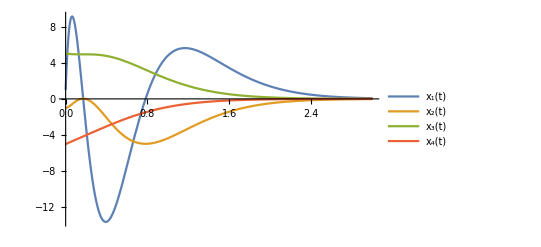

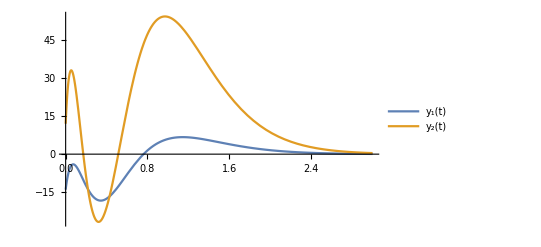

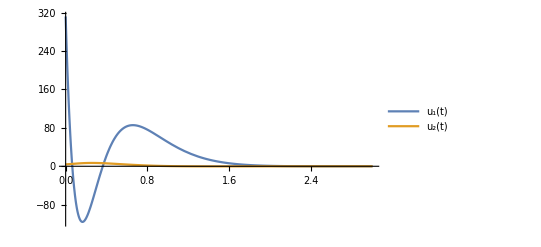

```mathematica
Clear[v];
x[t_]:=Array[Subscript[x, #][t] &,Length[A]]
y[t_]:=c.x[t];
v[t_]:={0, 0}
u[t_]=v[t]-K.x[t];
ClosedLoopEq=Thread[D[x[t],t]==(A-b.K).x[t]+b . v[t]//Chop];ColumnForm[ClosedLoopEq]
IC=Thread[x[0]=={1,-1, 5 ,-5}];
tmax=3;
CLSol=NDSolve[{ClosedLoopEq,IC}//Flatten,x[t],{t,0,tmax}];
Plot[{Evaluate[x[t]/.CLSol]},{t,0,tmax}, PlotRange->All, PlotLegends->{ x[t]}]
Plot[{Evaluate[c . x[t]/.CLSol]},{t,0,tmax}, PlotRange->All, PlotLegends->{ "y_1(t)","y_2(t)"}]
Plot[{Evaluate[-K.x[t]/.CLSol]},{t,0,tmax}, PlotRange->All, PlotLegends->{ "u_1(t)", "u_2(t)"}]
```

## iii)

```mathematica
Q=({{40, 40, 0, 0}, {40, 100, 0, 0}, {0, 0, 160, 32}, {0, 0, 32, 200}}); Sf=({{1000, 0, 0, 0}, {0, 500, 0, 0}, {0, 0, 800, 0}, {0, 0, 0, 1000}}); R=({{4, 0}, {0, 10}});
```

```mathematica
B=b; C1=c;
n=Length[A];
```

```mathematica
Sr=RiccatiSolve[{A,B},{Q,R}]//N// Chop;
Sr //MatrixForm
```

(27.883 | 77.1825 | 0 | 0
77.1825 | 247.073 | 0 | 0
0 | 0 | 25.4959 | 28.9898
0 | 0 | 28.9898 | 179.873)

```mathematica
PositiveDefiniteMatrixQ[Sr]
```

True

```mathematica
Eigenvalues[Sr]//N
```

{271.523,185.138,20.2316,3.43242}

```mathematica
Ko=(Inverse[R].Bᵀ .Sr)//FullSimplify;
Ko //MatrixForm
```

(6.97074 | 19.2956 | 0. | 0.
0. | 0. | 2.54959 | 2.89898)

```mathematica
Eigenvalues[A-B.Ko]//Simplify //N
```

{-4.84632,-4.44827,-2.12442,-1.10132}

x_1'[t]==-6.97074 x_1[t]-10.2956 x_2[t]
x_2'[t]==1. x_1[t]
x_3'[t]==-5.54959 x_3[t]-4.89898 x_4[t]
x_4'[t]==1. x_3[t]

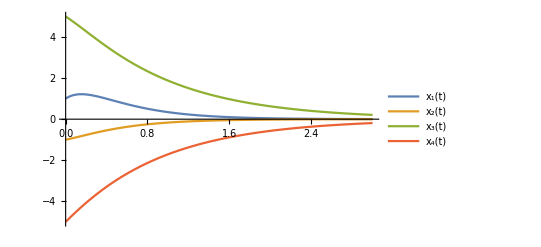

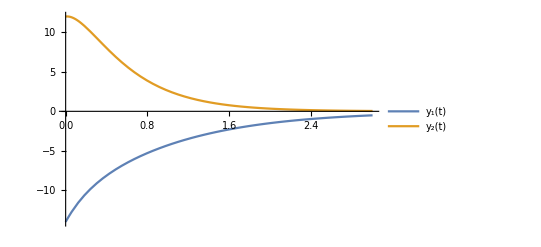

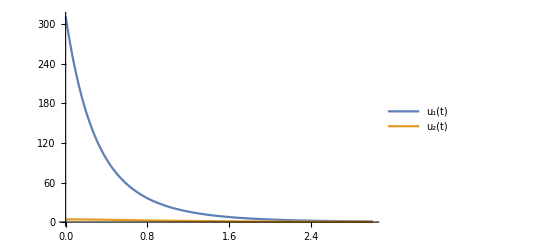

```mathematica
Clear[v];
x[t_]:=Array[Subscript[x, #][t] &,Length[A]]
y[t_]:=c.x[t];
v[t_]:={0, 0}
u[t_]=v[t]-Ko.x[t];
ClosedLoopEq=Thread[D[x[t],t]==(A-b.Ko).x[t]+b . v[t]//Chop];ColumnForm[ClosedLoopEq]
IC=Thread[x[0]=={1,-1, 5 ,-5}];
tmax=3;
CLSol=NDSolve[{ClosedLoopEq,IC}//Flatten,x[t],{t,0,tmax}];
Plot[{Evaluate[x[t]/.CLSol]},{t,0,tmax}, PlotRange->All, PlotLegends->{ x[t]}]
Plot[{Evaluate[c . x[t]/.CLSol]},{t,0,tmax}, PlotRange->All, PlotLegends->{ "y_1(t)","y_2(t)"}]
Plot[{Evaluate[-K.x[t]/.CLSol]},{t,0,tmax}, PlotRange->All, PlotLegends->{ "u_1(t)", "u_2(t)"}]
```

## Way better solution than part ii! Transient response is improved!

## iv)

## This time K will change with time. (tf --/-->∞)

```mathematica
A
```

{{0,9,0,0},{1,0,0,0},{0,0,-3,-2},{0,0,1,0}}

```mathematica
C1=C1 //N
```

{{1.,0.,3.,6.},{3.,-9.,0.5,0.5}}

```mathematica
Clear[S]
```

```mathematica
S[t_]:=Array[Subscript[S,Sequence@@Through[{Min,Max}[##]]][t]&,{Length[A],Length[A]}]
S[t]
(*LHRE=D[S[t],t]+S[t].A-S[t].B.Inverse[R].Bᵀ.S[t]+C1ᵀ.Q.C1+Aᵀ.S[t] *)
```

{{S_(1,1)[t],S_(1,2)[t],S_(1,3)[t],S_(1,4)[t]},{S_(1,2)[t],S_(2,2)[t],S_(2,3)[t],S_(2,4)[t]},{S_(1,3)[t],S_(2,3)[t],S_(3,3)[t],S_(3,4)[t]},{S_(1,4)[t],S_(2,4)[t],S_(3,4)[t],S_(4,4)[t]}}

```mathematica
LHRE=D[S[t],t]+S[t].A-S[t].B.Inverse[R].Bᵀ.S[t]+Q+Aᵀ.S[t]
```

(S_(1,1)'(t)-1/4 (S_(1,1)(t))^2-1/10 (S_(1,3)(t))^2+2 S_(1,2)(t)+40 | S_(1,2)'(t)-1/4 S_(1,2)(t) S_(1,1)(t)+9 S_(1,1)(t)+S_(2,2)(t)-1/10 S_(1,3)(t) S_(2,3)(t)+40 | S_(1,3)'(t)-1/4 S_(1,1)(t) S_(1,3)(t)-1/10 S_(3,3)(t) S_(1,3)(t)-3 S_(1,3)(t)+S_(1,4)(t)+S_(2,3)(t) | S_(1,4)'(t)-1/10 S_(3,4)(t) S_(1,3)(t)-2 S_(1,3)(t)-1/4 S_(1,1)(t) S_(1,4)(t)+S_(2,4)(t)
S_(1,2)'(t)-1/4 S_(1,2)(t) S_(1,1)(t)+9 S_(1,1)(t)+S_(2,2)(t)-1/10 S_(1,3)(t) S_(2,3)(t)+40 | S_(2,2)'(t)-1/4 (S_(1,2)(t))^2+18 S_(1,2)(t)-1/10 (S_(2,3)(t))^2+100 | S_(2,3)'(t)-1/4 S_(1,2)(t) S_(1,3)(t)+9 S_(1,3)(t)-3 S_(2,3)(t)+S_(2,4)(t)-1/10 S_(2,3)(t) S_(3,3)(t) | S_(2,4)'(t)-1/4 S_(1,2)(t) S_(1,4)(t)+9 S_(1,4)(t)-2 S_(2,3)(t)-1/10 S_(2,3)(t) S_(3,4)(t)
S_(1,3)'(t)-1/4 S_(1,1)(t) S_(1,3)(t)-1/10 S_(3,3)(t) S_(1,3)(t)-3 S_(1,3)(t)+S_(1,4)(t)+S_(2,3)(t) | S_(2,3)'(t)-1/4 S_(1,2)(t) S_(1,3)(t)+9 S_(1,3)(t)-3 S_(2,3)(t)+S_(2,4)(t)-1/10 S_(2,3)(t) S_(3,3)(t) | S_(3,3)'(t)-1/4 (S_(1,3)(t))^2-1/10 (S_(3,3)(t))^2-6 S_(3,3)(t)+2 S_(3,4)(t)+160 | S_(3,4)'(t)-1/4 S_(1,3)(t) S_(1,4)(t)-2 S_(3,3)(t)-1/10 S_(3,3)(t) S_(3,4)(t)-3 S_(3,4)(t)+S_(4,4)(t)+32
S_(1,4)'(t)-1/10 S_(3,4)(t) S_(1,3)(t)-2 S_(1,3)(t)-1/4 S_(1,1)(t) S_(1,4)(t)+S_(2,4)(t) | S_(2,4)'(t)-1/4 S_(1,2)(t) S_(1,4)(t)+9 S_(1,4)(t)-2 S_(2,3)(t)-1/10 S_(2,3)(t) S_(3,4)(t) | S_(3,4)'(t)-1/4 S_(1,3)(t) S_(1,4)(t)-2 S_(3,3)(t)-1/10 S_(3,3)(t) S_(3,4)(t)-3 S_(3,4)(t)+S_(4,4)(t)+32 | S_(4,4)'(t)-1/4 (S_(1,4)(t))^2-1/10 (S_(3,4)(t))^2-4 S_(3,4)(t)+200)

```mathematica
UpperElements[M_]:=Flatten[Table[M[[i,j]],{i,Length[M]},{j,i,Length[M]}]]
LHREnD=UpperElements[LHRE];
Ov=ConstantArray[0,Length[LHREnD]];
```

```mathematica
RE=Thread[LHREnD==Ov]
Sv[t_]:=UpperElements[S[t]]
```

{40-1/4 (S_(1,1)[t])^2+2 S_(1,2)[t]-1/10 (S_(1,3)[t])^2+S_(1,1)'[t]==0,40+9 S_(1,1)[t]-1/4 S_(1,1)[t] S_(1,2)[t]+S_(2,2)[t]-1/10 S_(1,3)[t] S_(2,3)[t]+S_(1,2)'[t]==0,-3 S_(1,3)[t]-1/4 S_(1,1)[t] S_(1,3)[t]+S_(1,4)[t]+S_(2,3)[t]-1/10 S_(1,3)[t] S_(3,3)[t]+S_(1,3)'[t]==0,-2 S_(1,3)[t]-1/4 S_(1,1)[t] S_(1,4)[t]+S_(2,4)[t]-1/10 S_(1,3)[t] S_(3,4)[t]+S_(1,4)'[t]==0,100+18 S_(1,2)[t]-1/4 (S_(1,2)[t])^2-1/10 (S_(2,3)[t])^2+S_(2,2)'[t]==0,9 S_(1,3)[t]-1/4 S_(1,2)[t] S_(1,3)[t]-3 S_(2,3)[t]+S_(2,4)[t]-1/10 S_(2,3)[t] S_(3,3)[t]+S_(2,3)'[t]==0,9 S_(1,4)[t]-1/4 S_(1,2)[t] S_(1,4)[t]-2 S_(2,3)[t]-1/10 S_(2,3)[t] S_(3,4)[t]+S_(2,4)'[t]==0,160-1/4 (S_(1,3)[t])^2-6 S_(3,3)[t]-1/10 (S_(3,3)[t])^2+2 S_(3,4)[t]+S_(3,3)'[t]==0,32-1/4 S_(1,3)[t] S_(1,4)[t]-2 S_(3,3)[t]-3 S_(3,4)[t]-1/10 S_(3,3)[t] S_(3,4)[t]+S_(4,4)[t]+S_(3,4)'[t]==0,200-1/4 (S_(1,4)[t])^2-4 S_(3,4)[t]-1/10 (S_(3,4)[t])^2+S_(4,4)'[t]==0}

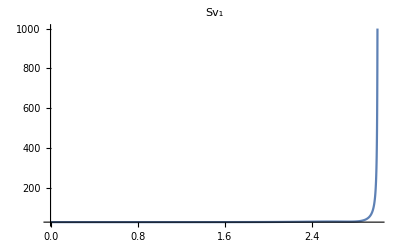
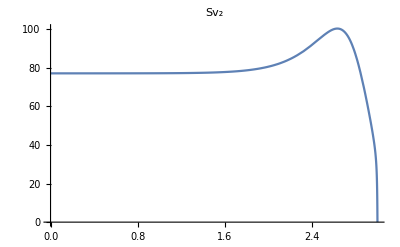
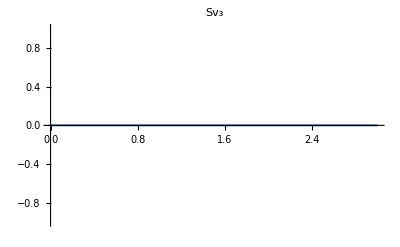
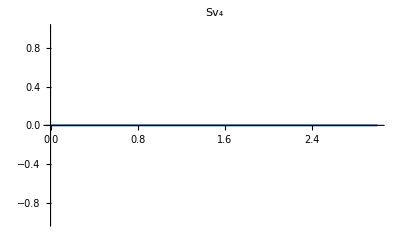
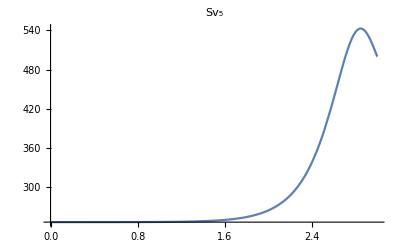
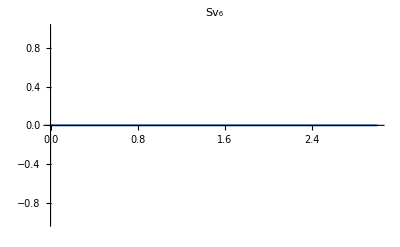
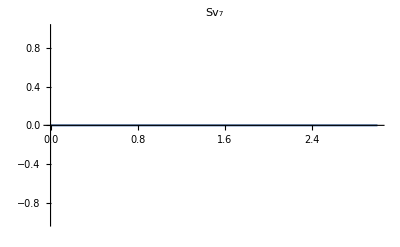
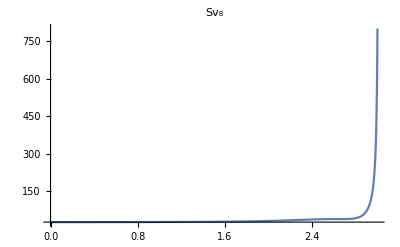

```mathematica
tf=3;
SolS=NDSolve[{RE,Thread[Sv[tf]==UpperElements[Sf]]}//Flatten,Sv[t],{t,0,tf}, Method->"StiffnessSwitching"];
Table[Plot[Evaluate[Sv[t][[i]]/.SolS],{t,0,tf}, PlotRange->{{0,tf},All},PlotLabel->Subscript["Sv", i]],{i,1,Length[Sv[t]]}]
```

{{1/4 S_(1,1)[t],1/4 S_(1,2)[t],1/4 S_(1,3)[t],1/4 S_(1,4)[t]},{1/10 S_(1,3)[t],1/10 S_(2,3)[t],1/10 S_(3,3)[t],1/10 S_(3,4)[t]}}

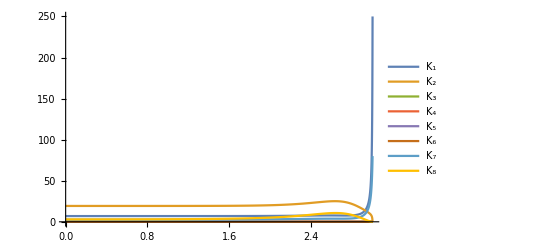

```mathematica
Clear[Ko]
Ko[t_]:=(Inverse[R].Bᵀ .S[t])
Ko[t]
Plot[Evaluate[Ko[t]/.SolS],{t,0,tf}, PlotRange->{{0,tf},All},PlotLegends->{"K_1","K_2","K_3","K_4","K_5","K_6","K_7","K_8" }]
```

## 2 of the values in K matrix spikes at the last second. This will cause a diversion from optimality

```mathematica
uop2[t_]:=-Ko[t].x[t]
yop[t_]:=C1.x[t];
```

```mathematica
StEqn2=Thread[D[x[t],t]==A.x[t]+B.uop2[t]]//Chop;
ColumnForm[StEqn2]
IC=Thread[x[0]=={1,-1,5,-5}]//Flatten
```

x_1'[t]==9 x_2[t]-1/4 x_1[t] S_(1,1)[t]-1/4 x_2[t] S_(1,2)[t]-1/4 x_3[t] S_(1,3)[t]-1/4 x_4[t] S_(1,4)[t]
x_2'[t]==x_1[t]
x_3'[t]==-3 x_3[t]-2 x_4[t]-1/10 x_1[t] S_(1,3)[t]-1/10 x_2[t] S_(2,3)[t]-1/10 x_3[t] S_(3,3)[t]-1/10 x_4[t] S_(3,4)[t]
x_4'[t]==x_3[t]

{x_1[0]==1,x_2[0]==-1,x_3[0]==5,x_4[0]==-5}

```mathematica
SolStEqn2=NDSolve[{StEqn2,IC}/.SolS,x[t],{t,0,tf}]//Flatten;
```

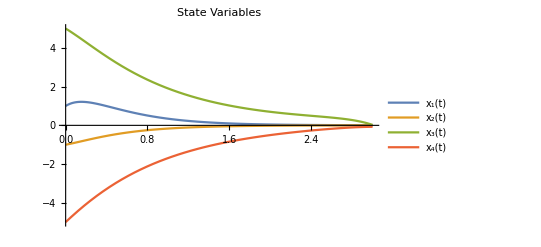

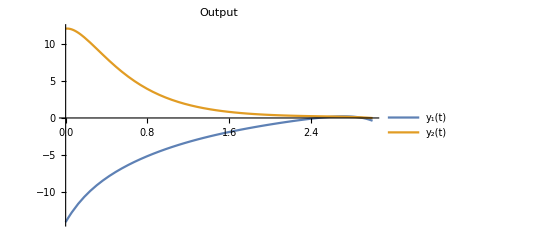

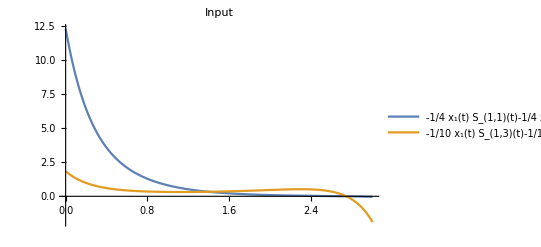

```mathematica
Plot[Evaluate[x[t]/.SolStEqn2],{t,0,tf}, PlotRange->All,PlotLegends->x[t],PlotLabel->"State Variables"]
Plot[Evaluate[yop[t]/.SolStEqn2/.SolS],{t,0,tf}, PlotRange->All,PlotLegends->y[t],PlotLabel->"Output"]
Plot[Evaluate[uop2[t]/.SolStEqn2/. SolS],{t,0,tf}, PlotRange->All,PlotLegends->u[t],PlotLabel->"Input"]
```

## LQR in the part iii) the best solution in terms of optimality. This one loses optimality while it is getting closer to final time tf!

## v)

```mathematica
Om=Join[C1ᵀ,Aᵀ.C1ᵀ, (Aᵀ.Aᵀ).C1ᵀ,(Aᵀ.Aᵀ.Aᵀ).C1ᵀ, 2]ᵀ ;
Om // MatrixForm
MatrixRank[Om]
```

(1. | 0. | 3. | 6.
3. | -9. | 0.5 | 0.5
0. | 9. | -3. | -6.
-9. | 27. | -1. | -1.
9. | 0. | 3. | 6.
27. | -81. | 2. | 2.
0. | 81. | -3. | -6.
-81. | 243. | -4. | -4.)

4

I forgot that this method only works for SISO systems (need inverse[Om]). I just left it here. I attempted this way and failed.

```mathematica
Inverse[Om]
```

Inverse::matsq: Argument {{1.,0.,3.,6.},{3.,-9.,0.5,0.5},{0.,9.,-3.,-6.},{-9.,27.,-1.,-1.},{9.,0.,3.,6.},{27.,-81.,2.,2.},{0.,81.,-3.,-6.},{-81.,243.,-4.,-4.}} at position 1 is not a non-empty square matrix.

Inverse[{{1.,0.,3.,6.},{3.,-9.,0.5,0.5},{0.,9.,-3.,-6.},{-9.,27.,-1.,-1.},{9.,0.,3.,6.},{27.,-81.,2.,2.},{0.,81.,-3.,-6.},{-81.,243.,-4.,-4.}}]

Observable!

```mathematica
I4=IdentityMatrix[4];
a[s]=Det[s I4-A]//Expand
```

-18-27 s-7 s^2+3 s^3+s^4

```mathematica
αo[s]=(s+16)^2(s+20)^2//Expand//N
```

102400.+23040. s+1936. s^2+72. s^3+s^4

```mathematica
Ut=({{1, 3, -7, -27}, {0, 1, 3, -7}, {0, 0, 1, 3}, {0, 0, 0, 1}});
```

```mathematica
αoc=Reverse[Drop[CoefficientList[αo[s],s],-1]]//N //Chop
```

{72.,1936.,23040.,102400.}

```mathematica
ac=Reverse[Drop[CoefficientList[a[s],s],-1]]
```

{3,-7,-27,-18}

```mathematica
Lt={(αoc-ac).Inverse[Ut].Inverse[Omᵀ]};
```

```mathematica
Ut.Omᵀ //MatrixForm
```

(-182. | -41. | 210. | 106. | -174. | -284.
-33. | -11. | 42. | 31. | -33. | -89.
21. | 2. | -21. | -4. | 21. | 8.
6. | 0.5 | -6. | -1. | 6. | 2.)

## I did coefficient matching but I struggled with the mathematica syntax. I used python to do the coefficient matching by giving poles -16,-16, -20, -20 and found the L.

```mathematica
L1=({{1009.9678571428571428571428571429, 1009.9678571428571428571428571429}, {724.28293650793650793650793650794, 724.28293650793650793650793650794}, {54187.575, 54187.575}, {-28785.975, -28785.975}});
```

```mathematica
Eigenvalues[A-L1.C1]
```

{-20.+0.00371062 ⅈ,-20.-0.00371062 ⅈ,-16.+0.00299783 ⅈ,-16.-0.00299783 ⅈ}

## Given L matrix placed desired position. There is a small imaginary value and they are extremely high numbers. I remember we use some matrices in the LSA class but I couldn’t get the class files. I wanted to check with the MATLAB place() function to see what is the answer there. Found as follow:

```mathematica
L=({{109.25, -73.25}, {36.4167, 0.1389}, {23.75, 984.25}, {-23.75, -480.25}});
```

```mathematica
K //MatrixForm  (* K from pole placement (part 2) *)
```

(18 | 130 | 360 | 400
0 | -1 | -3 | -2)

```mathematica
Ac=A-L.C1;
```

## Eqs trial without noise

```mathematica
xo[t_]:={xo1[t],xo2[t],xo3[t], xo4[t]};u[t_]={u1[t], u2[t]}; 
EqObserver=Thread[xo'[t]==Ac.xo[t]+L.y[t]+B.u[t]]//Chop//Flatten;
TableForm[EqObserver]
```

xo1'[t]==u1[t]+110.5 xo1[t]-650.25 xo2[t]-291.125 xo3[t]-618.875 xo4[t]+109.25 y_1[t]-73.25 y_2[t]
xo2'[t]==-35.8334 xo1[t]+1.2501 xo2[t]-109.32 xo3[t]-218.57 xo4[t]+36.4167 y_1[t]+0.1389 y_2[t]
xo3'[t]==u2[t]-2976.5 xo1[t]+8858.25 xo2[t]-566.375 xo3[t]-636.625 xo4[t]+23.75 y_1[t]+984.25 y_2[t]
xo4'[t]==1464.5 xo1[t]-4322.25 xo2[t]+312.375 xo3[t]+382.625 xo4[t]-23.75 y_1[t]-480.25 y_2[t]

```mathematica
Length[x[t]]
```

4

```mathematica
Length[v[t]]
```

2

```mathematica
W=0.1IdentityMatrix[Length[x[t]]];
 Θ=0.01IdentityMatrix[Length[v[t]]];
```

### Plant Noise:

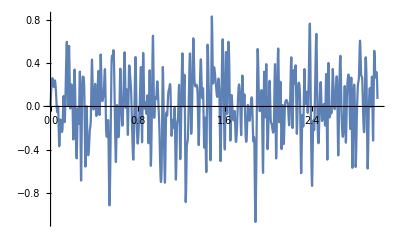

Mean: -0.0129999 
Variance: 0.0799231

```mathematica
tmax=tf;step=0.01;σW=√W[[1,1]];
g=Interpolation[Thread[{Range[0,tmax,step],Join[{0},RandomReal[NormalDistribution[0,σW],tmax/step]]}],t];
Plot[g,{t,0,tmax}]
Print["Mean: ",Mean[RandomReal[NormalDistribution[0,σW],tmax/step]]," \nVariance: ",Variance[RandomReal[NormalDistribution[0,σW],tmax/step]]]
```

### Sensor Noise

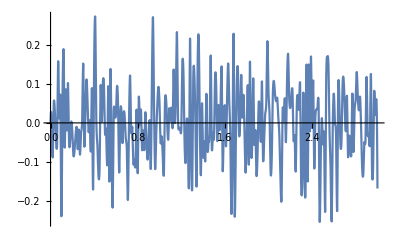

Mean: 0.00685842 
Variance: 0.00974751

```mathematica
σθ=√Θ[[1,1]];
θ=Interpolation[Thread[{Range[0,tmax,step],Join[{0},RandomReal[NormalDistribution[0,σθ],tmax/step]]}],t];
Plot[θ,{t,0,tmax}]
Print["Mean: ",Mean[RandomReal[NormalDistribution[0,σθ],tmax/step]]," \nVariance: ",Variance[RandomReal[NormalDistribution[0,σθ],tmax/step]]]
```

```mathematica
Clear[u]
```

```mathematica
xov[t_]:=Array[Subscript[xo, #][t]&,Length[A]];
uoc[t_]:=-K.xov[t]
yhat[t_]:=C1.xov[t]
ynoise[t_]:=C1.x[t]+ConstantArray[θ,Length[y[t]]]
```

```mathematica
EqObserverOp=Thread[xov'[t]==A.xov[t]+B.uoc[t]+L.(ynoise[t]-yhat[t])]//Chop//Flatten;
EqObsControllerOp=Thread[x'[t]==(A-B.K).x[t]+B.K.(x[t]-xov[t])+ConstantArray[g,Length[x[t]]]];
AllEqnOp={EqObserverOp,EqObsControllerOp}//Chop//Flatten//Simplify;
ColumnForm[AllEqnOp];
IC=Thread[x[0]=={1,-1,5,-5}]//Flatten;
ICo=Thread[xov[0]=={0,0,0,0}]//Flatten;
```

```mathematica
SolObsControllerOp=NDSolve[{AllEqnOp,IC,ICo}//Flatten,{x[t],xov[t]}//Flatten,{t,0,tf}]//Flatten;
```

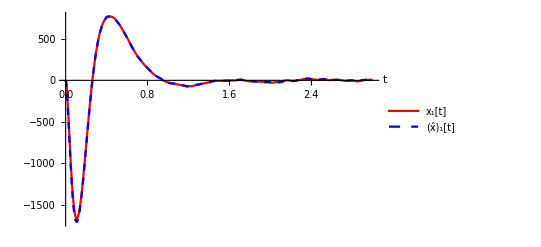
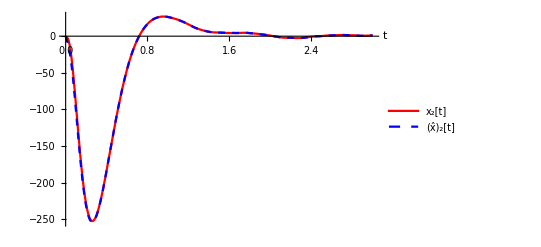
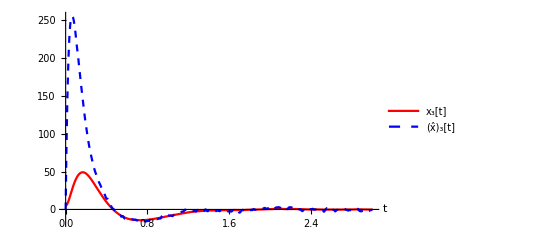
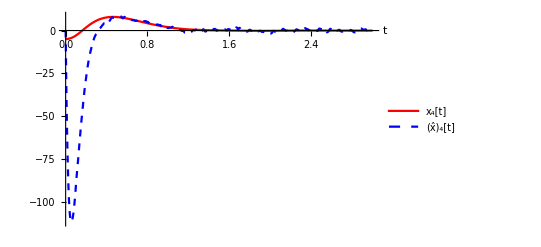

```mathematica
Table[Plot[Evaluate[{x[t][[i]],xov[t][[i]]}/.SolObsControllerOp],{t,0,tf},PlotStyle->{{Red},{Dashed,Blue}},PlotRange->All,AxesLabel->{"t"},PlotLegends->{ToString[Subscript["x", i], StandardForm]<>"[t]",ToString[Subscript["x̂", i], StandardForm]<>"[t]"}], {i, 1, Length[x[t]]}]//TableForm
```

## Error is very large at the beginning for states 3 and 4.

## vi)

### Solve the Filter Algebraic Riccati Equation :

The steady state error covariance matrix Σ:

```mathematica
W=0.1IdentityMatrix[Length[x[t]]];
 Θ=0.01IdentityMatrix[Length[v[t]]];
Σ=RiccatiSolve[{Aᵀ,C1ᵀ},{W, Θ}];
Print["Σ = ",Σ//MatrixForm]
```

Σ = (2.20641 | 0.721383 | 0.0526951 | -0.333838
0.721383 | 0.239227 | 0.0177511 | -0.109225
0.0526951 | 0.0177511 | 0.0220575 | -0.0167187
-0.333838 | -0.109225 | -0.0167187 | 0.0597287)

```mathematica
Lop=Σ .C1ᵀ.Inverse[Θ];
Print["L_opt = ",Lop//MatrixForm]
```

L_opt = (36.1468 | -1.37801
11.9284 | -3.46262
1.85555 | 0.0994942
-2.56226 | 0.301816)

```mathematica
P=RiccatiSolve[{A,B},{Q, R}]//N;
Print["P = ",P//MatrixForm]
```

P = (27.883 | 77.1825 | 0. | 0.
77.1825 | 247.073 | 0. | 0.
0. | 0. | 25.4959 | 28.9898
0. | 0. | 28.9898 | 179.873)

### Plant Noise:

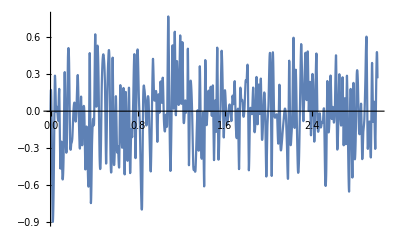

Mean: -0.0148233 
Variance: 0.112052

```mathematica
tmax=tf;step=0.01;σW=√W[[1,1]];
g=Interpolation[Thread[{Range[0,tmax,step],Join[{0},RandomReal[NormalDistribution[0,σW],tf/step]]}],t];
Plot[g,{t,0,tf}]
Print["Mean: ",Mean[RandomReal[NormalDistribution[0,σW],tf/step]]," \nVariance: ",Variance[RandomReal[NormalDistribution[0,σW],tf/step]]]
```

### Sensor Noise

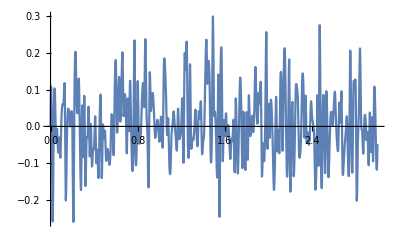

Mean: 0.00550301 
Variance: 0.0100085

```mathematica
σθ=√Θ[[1,1]];
θ=Interpolation[Thread[{Range[0,tmax,step],Join[{0},RandomReal[NormalDistribution[0,σθ],tf/step]]}],t];
Plot[θ,{t,0,tf}]
Print["Mean: ",Mean[RandomReal[NormalDistribution[0,σθ],tf/step]]," \nVariance: ",Variance[RandomReal[NormalDistribution[0,σθ],tf/step]]]
```

#### Combined Observer - Controller Equations

### Build State Equation :

```mathematica
K
```

{{18,130,360,400},{0,-1,-3,-2}}

```mathematica
Ko=(Inverse[R].Bᵀ .Sr)//FullSimplify;
Ko //MatrixForm
```

(6.97074 | 19.2956 | 0. | 0.
0. | 0. | 2.54959 | 2.89898)

```mathematica
uop[t_]:=-Ko.x[t]
yop[t_]:=C1.x[t];
StEqn=Thread[D[x[t],t]==A.x[t]+B.uop[t]]//Chop;
ColumnForm[StEqn]
IC=Thread[x[0]=={1,-1,5,-5}]//Flatten
```

x_1'[t]==-6.97074 x_1[t]-10.2956 x_2[t]
x_2'[t]==x_1[t]
x_3'[t]==-5.54959 x_3[t]-4.89898 x_4[t]
x_4'[t]==x_3[t]

{x_1[0]==1,x_2[0]==-1,x_3[0]==5,x_4[0]==-5}

```mathematica
Clear[u]
```

```mathematica
xov[t_]:=Array[Subscript[xo, #][t]&,Length[A]];
uoc[t_]:=-Ko.xov[t]
yhat[t_]:=C1.xov[t]
ynoise[t_]:=C1.x[t]+ConstantArray[θ,Length[y[t]]]
```

```mathematica
EqObserverOp=Thread[xov'[t]==A.xov[t]+B.uoc[t]+Lop.(ynoise[t]-yhat[t])]//Chop//Flatten;
EqObsControllerOp=Thread[x'[t]==(A-B.Ko).x[t]+B.Ko.(x[t]-xov[t])+ConstantArray[g,Length[x[t]]]];
AllEqnOp={EqObserverOp,EqObsControllerOp}//Chop//Flatten//Simplify;
ColumnForm[AllEqnOp];
IC=Thread[x[0]=={1,-1,5,-5}]//Flatten;
ICo=Thread[xov[0]=={0,0,0,0}]//Flatten;
```

```mathematica
SolObsControllerOp=NDSolve[{AllEqnOp,IC,ICo}//Flatten,{x[t],xov[t]}//Flatten,{t,0,tf}]//Flatten;
```

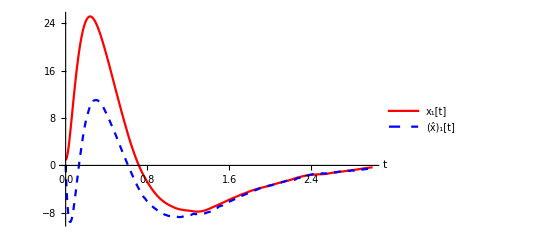
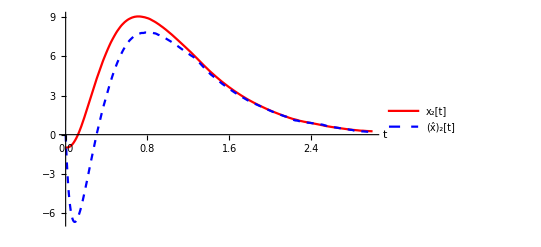
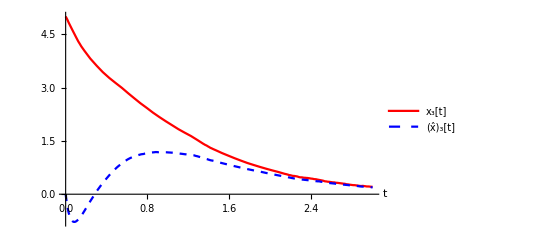
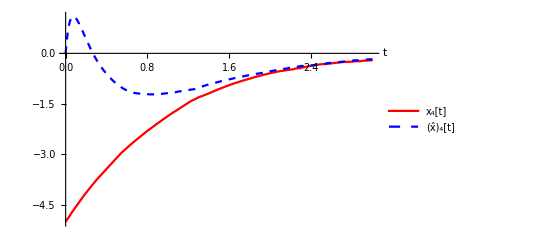

```mathematica
Table[Plot[Evaluate[{x[t][[i]],xov[t][[i]]}/.SolObsControllerOp],{t,0,tf},PlotStyle->{{Red},{Dashed,Blue}},PlotRange->All,AxesLabel->{"t"},PlotLegends->{ToString[Subscript["x", i], StandardForm]<>"[t]",ToString[Subscript["x̂", i], StandardForm]<>"[t]"}], {i, 1, Length[x[t]]}]//TableForm
```

## This response is better than the the first one (part v, given pole placement) since we see